```mathematica
(* test eigenvalues are (+a,-a),(+b,-b),(+c,-c), shifted to positive (+2a,0),(+2b,0),(a+b-c,a+b-c) *)
```

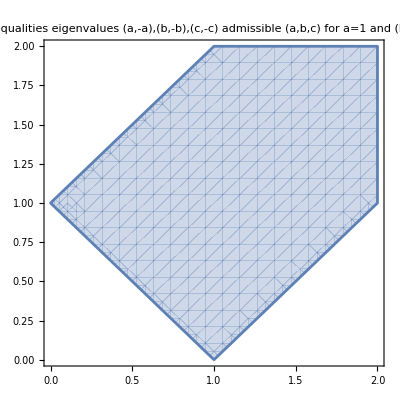

```mathematica
TriangleIneqs=RegionPlot[Abs[b-1]<=c<=1+b,{b,0,2},{c,0,2},PlotLabel->"Triangle inequalities \n eigenvalues (a,-a),(b,-b),(c,-c) \n admissible (a,b,c) for a=1 and (b,c)∈[0,2]×[0,2]"]
```

```mathematica
(*  γ1+γ2==α+β=k  *)
```

```mathematica
(*  γ2==k-γ1 with γ1≥max(α,β) && γ1<=α+β counting by ones  *)
```

```mathematica
(*  let l = γ1 = *)
```

```mathematica
(((a+b)^2-c^2)^(k-l) (-(a+b-c)^(1-k+2*l)+(a+b+c)^(1-k+2*l)))/(2 c)
```

```mathematica
(* let s = a+b *)
```

```mathematica
Sum[((s-c)^(k-l) (s+c)^(1+l)-(s-c)^(1+l) (s+c)^(k-l))/(2 c),{l,3,k}]
```

```mathematica
HookProduct[r1_,r2_]:=(Factorial[r1+1]Factorial[r1-r2]Factorial[r2])/Factorial[r1-r2+1]
```

```mathematica
Schur2[r1_,r2_,e1_,e2_]:=(e1^(r1+1)*e2^r2-e1^r2*e2^(r1+1))/(e1-e2)
```

```mathematica
Schur1[r_,e_]:=e^r
```

```mathematica
Schur2[l,k-l,1+x,1-x]/HookProduct[l,k-l]
```

((-(1-x)^(1+l) (1+x)^(k-l)+(1-x)^(k-l) (1+x)^(1+l)) (1-k+2 l)!)/(2 x (k-l)! (1+l)! (-k+2 l)!)

```mathematica
FullSimplify[FullSimplify[Sum[Simplify[Schur2[l,k-l,1+x,1-x]]/HookProduct[l,k-l],{l,m,k}]]/.{m->β,k->α+β}]
```

```mathematica
1/(2 x α! Gamma[2+β])(1-α+β) (-(1-x)^(β+1)(1+x)^α HypergeometricPFQ[{1,-α,3/2-α/2+β/2},{1/2-α/2+β/2,2+β},(-1+x)/(1+x)]+(1-x)^α (1+x)^(1+β) HypergeometricPFQ[{1,-α,3/2-α/2+β/2},{1/2-α/2+β/2,2+β},(1+x)/(-1+x)])
```

1/(2 x α! Gamma[2+β])(1-α+β) (-(1-x)^(1+β) (1+x)^α HypergeometricPFQ[{1,-α,3/2-α/2+β/2},{1/2-α/2+β/2,2+β},(-1+x)/(1+x)]+(1-x)^α (1+x)^(1+β) HypergeometricPFQ[{1,-α,3/2-α/2+β/2},{1/2-α/2+β/2,2+β},(1+x)/(-1+x)])

```mathematica
(* targets PSD eigenvalues (2a,0),(2b,0),(a+b+c,a+b-c) *)
LHSShiftAB[α_,β_]:=Function[{a,b},(2^(α+β)* If[α==0,1,a^α]*If[β==0,1, b^β])/(HookProduct[α,0]*HookProduct[β,0])]
Clear[RHSShiftAB]
RHSShiftAB[α_,β_]:=Function[{s,c},
Sum[
1/HookProduct[l,α+β-l]*
If[c==0,s^(α+β) (1+2 l-(α+β)),(* lhopital to get this c->0 limit *)
If[s==c&&α+β==l,(2s)^(α+β),(* edge case where a+b-c=0 *)
((s+c)^(l+1)(s-c)^(α+β-l) - (s+c)^(α+β-l)(s-c)^(l+1))/(2 c)]
],{l,Max[α,β],α+β}]](* l is the length of the first row, α+β-l is the length of the second row *)
```

```mathematica
(* adding the extra terms of the form Subscript[ϕ, (j)](2a,0)Subscript[ϕ, (k-j)](2b,0) *)
LHSShiftABTighter[α_,β_]:=
Function[{a,b},Sum[If[j>=Max[α,β]||j<=Min[α,β],(If[j==0,1,(2a)^j]*If[α+β-j==0,1,(2b)^(α+β-j)])/(HookProduct[j,0]*HookProduct[α+β-j,0]),0],{j,0,α+β,1}]]
```

```mathematica
IsInequalityNumericallySatisfied[α_,β_]:=
Function[{a,b,c},
Module[{rhs,lhs},
rhs=RHSShiftAB[α,β][a+b,c];
lhs=LHSShiftABTighter[α,β][a,b];
If[rhs==0, Return[lhs==0]];
lhs/rhs<=1
]
]
```

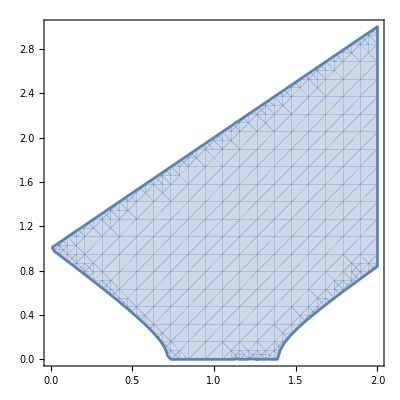

```mathematica
RegionPlot[
{
SatisfiedAtLevelK[20][1,b,c]
}
,{b,0,2},{c,0,3}]
```

```mathematica
(* targets PSD eigenvalues (2a,0),(2b,0),(a+b+c,a+b-c) *)
SatisfiedAtLevelK[k_]:=Function[{a,b,c},
(a+b-c≥0)(* inequalities implicitly work with PSD eigenvalues *)
&&Apply[And,Map[IsInequalityNumericallySatisfied[#,k-#][a,b,c]&,Range[0,k,1]]]
];
```

```mathematica
colorValuesForPlot=Map[ColorData["RedBlueTones"][#]&,Range[0.0,1.0,0.1]]
kValuesToPlot={2,4,6,8,10,12,14,16,18,20,∞};(**)
plotLegend=Map[StringJoin["k=",ToString[#]]&,kValuesToPlot];
plotLegend⟦Length[plotLegend]⟧="k=∞";
```

{RGBColor[0.450385, 0.157961, 0.217975],RGBColor[0.599449, 0.262748, 0.294618],RGBColor[0.721701, 0.434448, 0.400225],RGBColor[0.813151, 0.6177220000000001, 0.5077260000000001],RGBColor[0.865768, 0.767491, 0.623596],RGBColor[0.857126, 0.848339, 0.734867],RGBColor[0.7719229999999998, 0.8481949999999999, 0.811697],RGBColor[0.6197099999999998, 0.7811309999999999, 0.831119],RGBColor[0.433786, 0.670834, 0.793785],RGBColor[0.256859, 0.523007, 0.711644],RGBColor[0.139681, 0.311666, 0.550652]}

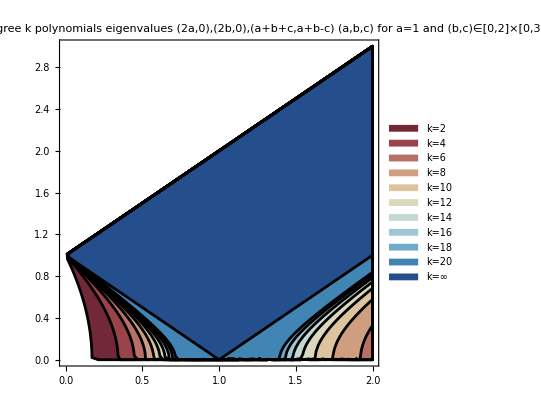

```mathematica
PolyTriangleIneqsFixedA=RegionPlot[
{
SatisfiedAtLevelK[kValuesToPlot⟦1⟧][1,b,c],
SatisfiedAtLevelK[kValuesToPlot⟦2⟧][1,b,c],
SatisfiedAtLevelK[kValuesToPlot⟦3⟧][1,b,c],
SatisfiedAtLevelK[kValuesToPlot⟦4⟧][1,b,c],
SatisfiedAtLevelK[kValuesToPlot⟦5⟧][1,b,c],
SatisfiedAtLevelK[kValuesToPlot⟦6⟧][1,b,c],
SatisfiedAtLevelK[kValuesToPlot⟦7⟧][1,b,c],
SatisfiedAtLevelK[kValuesToPlot⟦8⟧][1,b,c],
SatisfiedAtLevelK[kValuesToPlot⟦9⟧][1,b,c],
SatisfiedAtLevelK[kValuesToPlot⟦10⟧][1,b,c],
Abs[b-1]<=c<=1+b (*k=∞*)
}
,{b,0,2},{c,0,3},
PlotStyle->Map[Directive[Opacity[1],#]&,colorValuesForPlot],
BoundaryStyle->Black,
PlotLegends->plotLegend,
PlotLabel->"Constrained by degree k polynomials \n eigenvalues (2a,0),(2b,0),(a+b+c,a+b-c) \n (a,b,c) for a=1 and (b,c)∈[0,2]×[0,3]"]
```

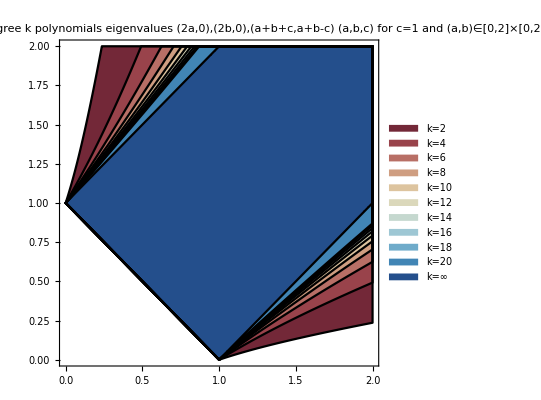

```mathematica
PolyTriangleIneqsFixedC=RegionPlot[
{
SatisfiedAtLevelK[kValuesToPlot⟦1⟧][a,b,1],
SatisfiedAtLevelK[kValuesToPlot⟦2⟧][a,b,1],
SatisfiedAtLevelK[kValuesToPlot⟦3⟧][a,b,1],
SatisfiedAtLevelK[kValuesToPlot⟦4⟧][a,b,1],
SatisfiedAtLevelK[kValuesToPlot⟦5⟧][a,b,1],
SatisfiedAtLevelK[kValuesToPlot⟦6⟧][a,b,1],
SatisfiedAtLevelK[kValuesToPlot⟦7⟧][a,b,1],
SatisfiedAtLevelK[kValuesToPlot⟦8⟧][a,b,1],
SatisfiedAtLevelK[kValuesToPlot⟦9⟧][a,b,1],
SatisfiedAtLevelK[kValuesToPlot⟦10⟧][a,b,1],
Abs[b-a]≤1≤a+b (*k=∞*)
}
,{a,0,2},{b,0,2},
PlotStyle->Map[Directive[Opacity[1],#]&,colorValuesForPlot],
BoundaryStyle->Black,
PlotLegends->plotLegend,
PlotLabel->"Constrained by degree k polynomials \n eigenvalues (2a,0),(2b,0),(a+b+c,a+b-c) \n (a,b,c) for c=1 and (a,b)∈[0,2]×[0,2]"]
```